### Preliminary AUC calculation

#### Phase Space Metric

```mathematica
Clear[dofxs,heavidandϵ]
(*dofxs[z_,zp_,s_:mW^2,sp_:mW^2]:= 2(s+sp) - 4 Min[z (1-z),zp(1-zp)] √(s/(z(1-z)) sp/(zp(1-zp)))*)
dofxs[z_,zp_,s_:mW^2,sp_:mW^2]:= 2(s+sp)-4If[z(1-z)>zp(1-zp), √(s sp(zp(1-zp))/(z (1-z))) ,√(s sp(z(1-z))/(zp (1-zp)))](*from appendix of smeared likelihood paper*)

heavidandϵfixedmJ[ϵ_?NumericQ,z_?NumericQ,zp_?NumericQ]:=HeavisideTheta[ϵ -√( 4 (1 -If[z(1-z)>zp(1-zp), √((zp(1-zp))/(z (1-z))) ,√((z(1-z))/(zp (1-zp)))]))](* ϵ in units of mW - assumes s = s' = Subscript[m, W]^2*)
heavidandϵ[ϵ_?NumericQ,z_?NumericQ,zp_?NumericQ,s_?NumericQ,sp_?NumericQ]:=Boole[ϵ^2 -dofxs[z,zp,s,sp]>0]
(* ϵ,s,sp in units of Subscript[m, signal](Subscript[m, W]) switch HeavisideTheta to Boole in NIntegrate*)
```

```mathematica
Clear[zpbounds]
"The values of zp (in terms of z) on the support of the SEMD heaviside";
zpbounds[ϵ_,z_,s_,sp_]:=Piecewise[{{<|"-"->{0,1/2},"+"->{1/2,1}|>,ϵ^2>=2 (s+sp)},{<|"-"->{1/2,1/2},"+"->{1/2,1/2}|>,ϵ^2<2 (s+sp)- 4 √(s sp)}},<|"-"->{1/2-√(1/4-a),1/2-√(1/4-b)},"+"->{1/2+√(1/4-b),1/2+√(1/4-a)}|>/.{b->Min[z(1-z)(16 s sp)/((2 (s+sp)-ϵ^2)^2),1/4],a->z(1-z)((2(s+sp)-ϵ^2)^2)/(16 s sp)}]
```

```mathematica
Assuming[{ϵ^2∈Reals,ϵ>0},zpbounds[ϵ,z,s,sp]//Simplify]
```

Piecewise[{{<|-→{0,1/2},+→{1/2,1}|>, ϵ^2≥2 (s+sp)}, {<|-→{1/2,1/2},+→{1/2,1/2}|>, ϵ^2<2 (s+sp-2 √(s sp))}, {<|-→{1/2-√(1/4-((1-z) z (2 (s+sp)-ϵ^2)^2)/(16 s sp)),1/2-√(1/4-Min[1/4,(16 s sp (1-z) z)/((2 (s+sp)-ϵ^2)^2)])},+→{1/2+√(1/4-Min[1/4,(16 s sp (1-z) z)/((2 (s+sp)-ϵ^2)^2)]),1/2+√(1/4-((1-z) z (2 (s+sp)-ϵ^2)^2)/(16 s sp))}|>, True}}]

```mathematica
1/2+√(1/4-(1-z)z)//Simplify//PowerExpand
1/2-√(1/4-(1-z)z)//Simplify//PowerExpand//Simplify
```

z

1-z

#### Unsmeared Phase Space Distributions

```mathematica
Clear[psignal,pquark,pgluon]
psignal[zp_?NumberQ]:=3/2 (zp^2+(1-zp)^2)(*we calculated this splitting function, for W -> ff' *)

pquark[zp_?NumberQ,pp_:10]:=((1+(1-zp)^2)/zp+(1+zp^2)/(1-zp))/(2 Log[pp^2//Simplify]-3/2)(*pp in units of mW/R - from Andrew's H->gg likelihood paper*)

pgluon[zp_?NumberQ,pp_:10]:= (CA (zp/(1-zp)+(1-zp)/zp+zp(1-zp)) + nf TR (zp^2+(1-zp)^2))/(2 CA Log[pp^2//Simplify]- 11/6 CA + 2/3 nf TR)/. {CA -> 3,CF->4/3,nf -> 3, TR->1/2 }(*pp in units of mW/R - pp >> mW/R and is farily irrelevant since in only changes a constant prefactor of the CDF*)
```

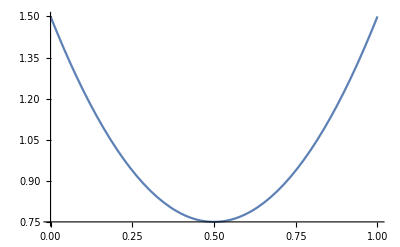

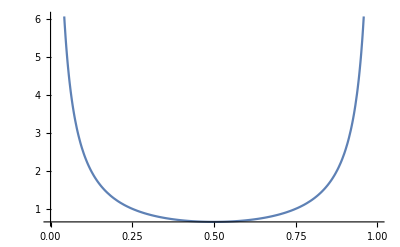

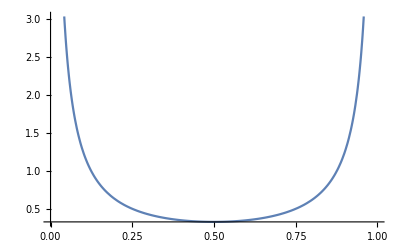

```mathematica
Plot[psignal[z],{z,0,1}]
Plot[pquark[zp],{zp,0,1}]
Plot[pgluon[zp],{zp,0,1}]
```

#### Smeared Phase Space Distributions

```mathematica
Clear[psignal,pquark,pgluon]

(*domain of integration is broken up for convergence (otherwise mathematica thinks it's 0)*)

(*psignal[z_?NumberQ,ϵ_?NumberQ]:=Quiet@Total@(NIntegrate[3/2 (zp^2+(1-zp)^2)heavidandϵ[ϵ,z,zp],{zp,#[[1]],#[[2]]}]&/@{{0,0.5},{0.5,1}})*)
psignalsmeared[z_?NumberQ,ϵ_?NumberQ]:=Quiet@(NIntegrate[3/2 (zp^2+(1-zp)^2)heavidandϵ[ϵ,z,zp,s,sp],{zp,0,1},{s,0.9,1.1},{sp,0.9,1.1}])(*we calculated this splitting function, for W -> ff' *)

pquarksmeared[z_?NumberQ,ϵ_?NumberQ,pp_:10/R]:=Quiet@Total@(NIntegrate[ ((1+(1-zp)^2)/zp+(1+zp^2)/(1-zp))/(2 Log[R^2 pp^2//Simplify]-3/2)heavidandϵ[ϵ,z,zp],{zp,#[[1]],#[[2]]}]&/@{{0,0.5},{0.5,1}})(*pp in units of mW - from Andrew's H->gg likelihood paper*)

pgluonsmeared[z_?NumberQ,ϵ_?NumberQ,pp_:10/R]:=Quiet@Total@(NIntegrate[ (CA (zp/(1-zp)+(1-zp)/zp+zp(1-zp)) + nf TR (zp^2+(1-zp)^2))/(2 CA Log[R^2 pp^2//Simplify]- 11/6 CA + 2/3 nf TR)heavidandϵ[ϵ,z,zp]/. {CA -> 3,CF->4/3,nf -> 3, TR->1/2 },{zp,#[[1]],#[[2]]}]&/@{{0,0.5},{0.5,1}})(*pp in units of mW - pp >> mW and is farily irrelevant since in only changes a constant prefactor of the CDF*)
```

```mathematica
psignalfsmeared=Interpolation[Table[{z,psignalsmeared[z,1]},{z,0.01,0.99,0.01}]]
```

$Aborted

```mathematica
"Interpolate the distributions"
psignalf=Interpolation[Table[{z,psignal[z,1]},{z,0.01,0.99,0.01}]]
pquarkf=Interpolation[Table[{z,pquark[z,1]},{z,0.01,0.99,0.01}]]
pgluonf=Interpolation[Table[{z,pgluon[z,1]},{z,0.01,0.99,0.01}]]
```

Interpolate the distributions

InterpolatingFunction[…]

NIntegrate::inumr: The integrand (((1+(1-zp)^2)/zp+(1+zp^2)/(1-zp)) heavidandϵ[1,0.01,zp])/(-3/2+2 Log[100]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,0.5}}.

NIntegrate::inumr: The integrand (((1+(1-zp)^2)/zp+(1+zp^2)/(1-zp)) heavidandϵ[1,0.01,zp])/(-3/2+2 Log[100]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.5,1}}.

NIntegrate::inumr: The integrand (((1+(1-zp)^2)/zp+(1+zp^2)/(1-zp)) heavidandϵ[1,0.02,zp])/(-3/2+2 Log[100]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,0.5}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand 0.129696 ((1.+(1.-1. zp)^2)/zp+(1.+zp^2)/(1.-1. zp)) heavidandϵ[1.,0.01,zp] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.,0.5}}.

NIntegrate::inumr: The integrand 0.129696 ((1.+(1.-1. zp)^2)/zp+(1.+zp^2)/(1.-1. zp)) heavidandϵ[1.,0.01,zp] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.5,1.}}.

NIntegrate::inumr: The integrand 0.129696 ((1.+(1.-1. zp)^2)/zp+(1.+zp^2)/(1.-1. zp)) heavidandϵ[1.,0.02,zp] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.,0.5}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

InterpolatingFunction[…]

NIntegrate::inumr: The integrand ((3 ((1-zp)/zp+zp/(1+Times[«2»])+(1-zp) zp)+3/2 ((1-zp)^2+zp^2)) heavidandϵ[1,0.01,zp])/(-9/2+6 Log[100]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,0.5}}.

NIntegrate::inumr: The integrand ((3 ((1-zp)/zp+zp/(1+Times[«2»])+(1-zp) zp)+3/2 ((1-zp)^2+zp^2)) heavidandϵ[1,0.01,zp])/(-9/2+6 Log[100]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.5,1}}.

NIntegrate::inumr: The integrand ((3 ((1-zp)/zp+zp/(1+Times[«2»])+(1-zp) zp)+3/2 ((1-zp)^2+zp^2)) heavidandϵ[1,0.02,zp])/(-9/2+6 Log[100]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,0.5}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand 0.043232 (3. ((1.-1. zp)/zp+zp/(1.+Times[«2»])+(1.-1. zp) zp)+1.5 ((1.-1. zp)^2+zp^2)) heavidandϵ[1.,0.01,zp] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.,0.5}}.

NIntegrate::inumr: The integrand 0.043232 (3. ((1.-1. zp)/zp+zp/(1.+Times[«2»])+(1.-1. zp) zp)+1.5 ((1.-1. zp)^2+zp^2)) heavidandϵ[1.,0.01,zp] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.5,1.}}.

NIntegrate::inumr: The integrand 0.043232 (3. ((1.-1. zp)/zp+zp/(1.+Times[«2»])+(1.-1. zp) zp)+1.5 ((1.-1. zp)^2+zp^2)) heavidandϵ[1.,0.02,zp] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.,0.5}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

InterpolatingFunction[…]

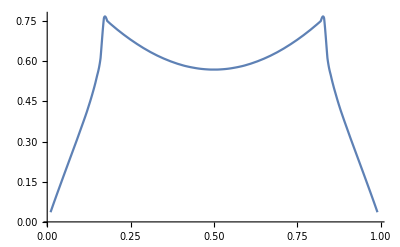

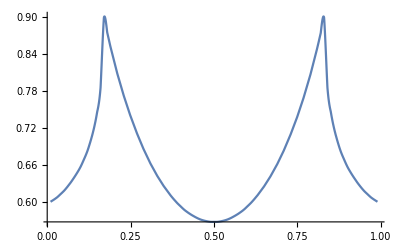

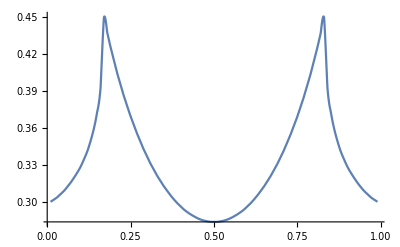

```mathematica
Plot[psignalf[z],{z,psignalf["Domain"][[1,1]],psignalf["Domain"][[1,2]]}]
Plot[pquarkf[zp],{zp,pquarkf["Domain"][[1,1]],pquarkf["Domain"][[1,2]]}]
Plot[pgluonf[zp],{zp,pgluonf["Domain"][[1,1]],pgluonf["Domain"][[1,2]]}]
```

#### get Σ(d)

```mathematica
"Now we want to interpolate the integrand of the CDF integral for a given pp (in units of mW/R) and s window (fractional). ";
Clear[psignalqCDFIntegrandf,psignalgCDFIntegrandf]

psignalqCDFIntegrandf[ϵ_,N_:10,Δs_:0.1,pp_:15]:=<|"+"->#["+"],"-"->#["-"]|>&@(Interpolation@Flatten[Table[zpb=zpbounds[ϵ,zp,s,sp];Table[{{ζz,zp,s,sp},Abs@(zpb[#][[2]]-zpb[#][[1]])psignal[zpb[#][[1]]+(zpb[#][[2]]-zpb[#][[1]])ζz] pquark[zp,pp](* HeavisideTheta[ϵ -√dofxs[zpb[#][[1]]+(zpb[#][[2]]-zpb[#][[1]])ζz,zp,s,sp]]*)},{ζz,0,1,1/N}],{zp,1/pp^2,1/2,(1/2-1/pp^2)1/N},{s,1-Δs,1+Δs,(2 Δs)/N},{sp,1-Δs,1+Δs,(2 Δs)/N}],{1,2,3,4}]&)(*ϵ,s,sp in units of Subscript[m, signal] - resctricting to the support of the Heavidandϵ (so no need to include it, in fact including it implies 0s on the boundary of the region of support which screws up the interpolations), includes jacobian for new coords*)

psignalgCDFIntegrandf[ϵ_,N_:10,Δs_:0.1,pp_:15]:=<|"+"->#["+"],"-"->#["-"]|>&@(Interpolation@Flatten[Table[zpb=zpbounds[ϵ,zp,s,sp];Table[{{ζz,zp,s,sp},Abs@(zpb[#][[2]]-zpb[#][[1]])psignal[zpb[#][[1]]+(zpb[#][[2]]-zpb[#][[1]])ζz] pgluon[zp,pp](* HeavisideTheta[ϵ -√dofxs[zpb[#][[1]]+(zpb[#][[2]]-zpb[#][[1]])ζz,zp,s,sp]]*)},{ζz,0,1,1/N}],{zp,1/pp^2,1/2,(1/2-1/pp^2)1/N},{s,1-Δs,1+Δs,(2 Δs)/N},{sp,1-Δs,1+Δs,(2 Δs)/N}],{1,2,3,4}]&)(*ϵ,s,sp in units of Subscript[m, signal] - resctricting to the support of the Heavidandϵ (so no need to include it, in fact including it implies 0s on the boundary of the region of support which screws up the interpolations), includes jacobian for new coords*)
```

```mathematica
Clear[GetΣqofd,GetΣgofd]
GetΣqofd[d_,N_:10]:=Module[{qfs,qf,dom,Σ},
qfs = psignalqCDFIntegrandf[d,N];
Σ = 0;
Do[
qf=qfs[i];
dom = qf["Domain"];
Σ+=Integrate[qf[z,zp,s,sp],{z,dom[[1,1]],dom[[1,2]]},{zp,dom[[2,1]],dom[[2,2]]},{s,dom[[3,1]],dom[[3,2]]},{sp,dom[[4,1]],dom[[4,2]]}];
(*Σ+=NIntegrate[qf[z,zp,s,sp],{z,dom[[1,1]],dom[[1,2]]},{zp,dom[[2,1]],dom[[2,2]]},{s,dom[[3,1]],dom[[3,2]]},{sp,dom[[4,1]],dom[[4,2]]},Method->"LocalAdaptive",MaxRecursion->12,AccuracyGoal->3,PrecisionGoal->3];*)
,{i,{"+","-"}}];
Σ
]
GetΣgofd[d_,N_:10]:=Module[{gfs,gf,dom,Σ},
gfs = psignalgCDFIntegrandf[d,N];
Σ = 0;
Do[
gf=gfs[i];
dom = gf["Domain"];
Σ+=Integrate[gf[z,zp,s,sp],{z,dom[[1,1]],dom[[1,2]]},{zp,dom[[2,1]],dom[[2,2]]},{s,dom[[3,1]],dom[[3,2]]},{sp,dom[[4,1]],dom[[4,2]]}];
(*Σ+=NIntegrate[qf[z,zp,s,sp],{z,dom[[1,1]],dom[[1,2]]},{zp,dom[[2,1]],dom[[2,2]]},{s,dom[[3,1]],dom[[3,2]]},{sp,dom[[4,1]],dom[[4,2]]},Method->"LocalAdaptive",MaxRecursion->12,AccuracyGoal->3,PrecisionGoal->3];*)
,{i,{"+","-"}}];
Σ
]
```

#### Test Plots at small d - Integrate

With Integrate

```mathematica
Σqofdtable =Monitor[Table[{d,GetΣqofd[d]},{d,1/8,3/8,1/(4 20)}],d];
```

-1.82901+1.97593 logd

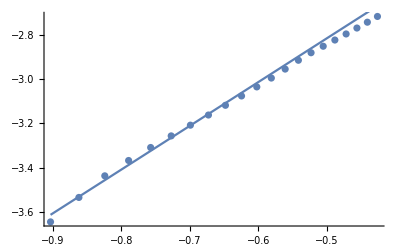

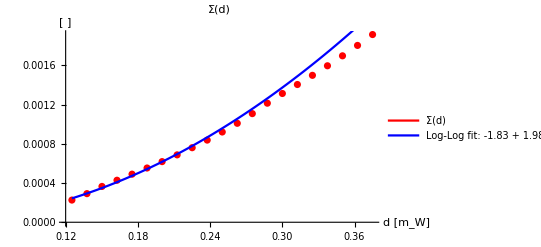

```mathematica
smalldfitfunc=Fit[(Log10@Σqofdtable)[[;;10]],{1,logd},{logd}]
Show[{ListPlot[Log10@Σqofdtable],Plot[%,{logd,Log10@(1/8),Log10@(3/8)}]}]
(*Show[{ListPlot[Σqofdtable],Plot[10^(%%/.logd->Log10[d]),{d,1/8,3/8}]}]*)
plot =Show[{ListPlot[Σqofdtable,PlotLabel->"Σ(d)",AxesLabel->{"d [m_W]","[ ]"},PlotStyle->Directive[Red,Thick]],Plot[10^(%%/.logd->Log10[d]),{d,1/8,3/8},PlotStyle->Blue,PlotLabel->"Small d fit to Σ(d)"]}];
Legended[plot,LineLegend[{Directive[Red,Thick],Blue},{"Σ(d)","Log-Log fit:\n"<>ToString[SetPrecision[smalldfitfunc,3]]}]]
```

```mathematica
SetPrecision[smalldfitfunc,2]
```

-1.3+2.6 logd

```mathematica
Σqofdtablesmaller =Monitor[Table[{d,GetΣqofd[d]},{d,0.01,0.2,0.01}],d];
```

-1.32415+2.57094 logd

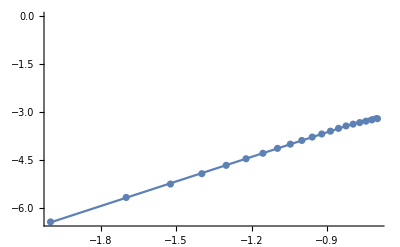

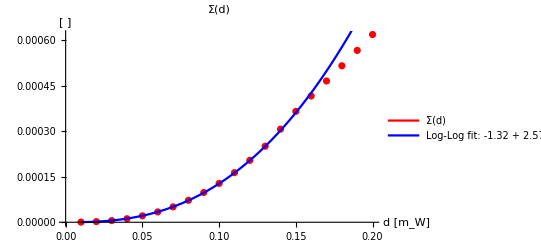

```mathematica
smalldfitfunc=Fit[(Log10@Σqofdtablesmaller)[[;;15]],{1,logd},{logd}]
Show[{ListPlot[Log10@Σqofdtablesmaller],Plot[%,{logd,Log10@0.01,Log10@0.2}]}]
Show[{ListPlot[Σqofdtablesmaller,PlotLabel->"Σ(d)",AxesLabel->{"d [m_W]","[ ]"},PlotStyle->Directive[Red,Thick]],Plot[10^(%%/.logd->Log10[d]),{d,0.01,0.2},PlotStyle->Blue,PlotLabel->"Small d fit to Σ(d)"]}];
Legended[%,LineLegend[{Directive[Red,Thick],Blue},{"Σ(d)","Log-Log fit:\n"<>ToString[SetPrecision[smalldfitfunc,3]]}]]
```

```mathematica
dom = {0.1,3,0.1};
Σqofdtablelarger =Monitor[Table[{d,GetΣqofd[d]},{d,dom[[1]],dom[[2]],dom[[3]]}],d];
```

-1.92664+1.92307 logd

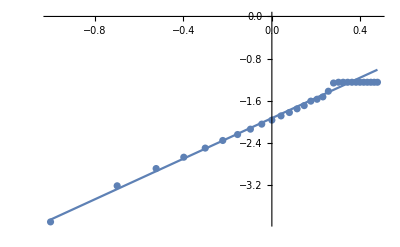

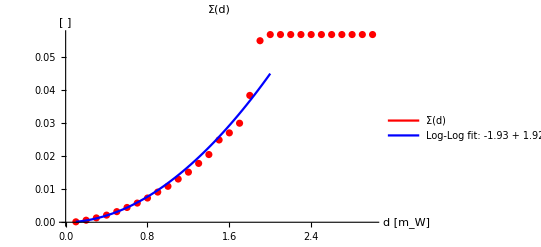

```mathematica
smalldfitfunc=Fit[(Log10@Σqofdtablelarger)[[;;20]],{1,logd},{logd}]
Show[{ListPlot[Log10@Σqofdtablelarger],Plot[%,{logd,Log10@dom[[1]],Log10@dom[[2]]}]}]
Show[{ListPlot[Σqofdtablelarger,PlotLabel->"Σ(d)",AxesLabel->{"d [m_W]","[ ]"},PlotStyle->Directive[Red,Thick]],Plot[10^(%%/.logd->Log10[d]),{d,dom[[1]],(2dom[[2]])/3},PlotStyle->Blue,PlotLabel->"Small d fit to Σ(d)"]}];
Legended[%,LineLegend[{Directive[Red,Thick],Blue},{"Σ(d)","Log-Log fit:\n"<>ToString[SetPrecision[smalldfitfunc,3]]}]]
```

### Deprecated

#### Phase Space distance CDF (quark and gluon background separately)

```mathematica
Clear[AUCqW]
AUCqW[d_?NumericQ]:= NIntegrate[psignalf[z]pquarkf[zp] heavidandϵ[d,z,zp],{z,psignalf["Domain"][[1,1]],psignalf["Domain"][[1,2]]},{zp,pquarkf["Domain"][[1,1]],pquarkf["Domain"][[1,2]]},PrecisionGoal->5,AccuracyGoal->5,Method->"LocalAdaptive"]

AUCgW[d_?NumericQ]:= NIntegrate[psignalf[z]pgluonf[zp] heavidandϵ[d,z,zp],{z,psignalf["Domain"][[1,1]],psignalf["Domain"][[1,2]]},{zp,pgluonf["Domain"][[1,1]],pgluonf["Domain"][[1,2]]},PrecisionGoal->5,AccuracyGoal->5,Method->"LocalAdaptive"]
```

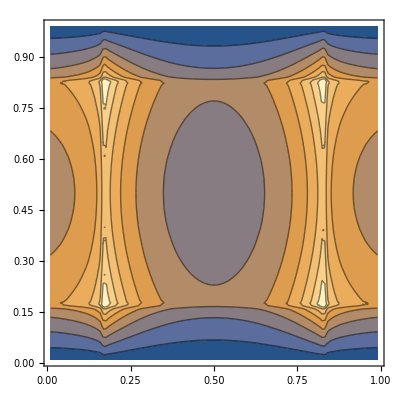

```mathematica
ContourPlot[pquarkf[zp]psignalf[z]heavidandϵ[4,z,zp],{zp,pquarkf["Domain"][[1,1]],pquarkf["Domain"][[1,2]]},{z,psignalf["Domain"][[1,1]],psignalf["Domain"][[1,2]]}]
```

```mathematica
"Interpolate the CDF in d for gluon and quark background - As andrew outlined in the H->gg paper, in general the background distribution will be some linear combination of the two. So these two cases define the endpoints of an interval describing the true background distribution.";

AUCqWtable=Table[{d,AUCqW[d]},{d,0.01,3,0.03}];
NormedAUCqWtable=Table[{AUCqWtable[[i,1]],AUCqWtable[[i,2]]/Max[AUCqWtable[[;;,2]]]},{i,Length[AUCqWtable]}];

AUCgWtable=Table[{d,AUCgW[d]},{d,0.01,3,0.03}];
NormedAUCgWtable=Table[{AUCgWtable[[i,1]],AUCgWtable[[i,2]]/Max[AUCgWtable[[;;,2]]]},{i,Length[AUCgWtable]}];

(*integrate from Subscript[z, min], and also integrate over s*)
```

NIntegrate::inumr: The integrand 0.129696 ((1.+(1.-1. zp)^2)/zp+(1.+zp^2)/(1.-1. zp)) heavidandϵ[1.,0.01,zp] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.,0.5}}.

NIntegrate::inumr: The integrand 0.129696 ((1.+(1.-1. zp)^2)/zp+(1.+zp^2)/(1.-1. zp)) heavidandϵ[1.,0.01,zp] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.5,1.}}.

NIntegrate::inumr: The integrand 0.129696 ((1.+(1.-1. zp)^2)/zp+(1.+zp^2)/(1.-1. zp)) heavidandϵ[1.,0.02,zp] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.,0.5}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

$Aborted

NIntegrate::inumr: The integrand 0.043232 (3. ((1.-1. zp)/zp+zp/(1.+Times[«2»])+(1.-1. zp) zp)+1.5 ((1.-1. zp)^2+zp^2)) heavidandϵ[1.,0.01,zp] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.,0.5}}.

NIntegrate::inumr: The integrand 0.043232 (3. ((1.-1. zp)/zp+zp/(1.+Times[«2»])+(1.-1. zp) zp)+1.5 ((1.-1. zp)^2+zp^2)) heavidandϵ[1.,0.01,zp] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.5,1.}}.

NIntegrate::inumr: The integrand 0.043232 (3. ((1.-1. zp)/zp+zp/(1.+Times[«2»])+(1.-1. zp) zp)+1.5 ((1.-1. zp)^2+zp^2)) heavidandϵ[1.,0.02,zp] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.,0.5}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

$Aborted

#### Plot the CDFs (and fit to parabolas)

0.00629337+0.970957 d^2

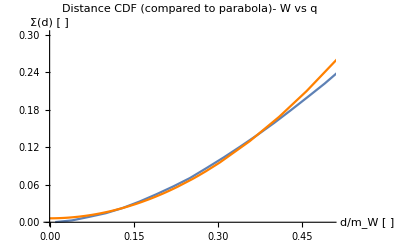

```mathematica
smalldfitfunc=Fit[NormedAUCqWtable[[;;15]],{1,d^2},{d}]
Show[{ListLinePlot[NormedAUCqWtable,AxesLabel->{"d/m_W [ ]","Σ(d) [ ]"},PlotLabel->"Distance CDF (compared to parabola)- W vs q",PlotRange->{{0,0.5},{0,0.3}}],Plot[smalldfitfunc,{d,0,2.5},PlotStyle->Orange]}]
```

0.00629337+0.970957 d^2

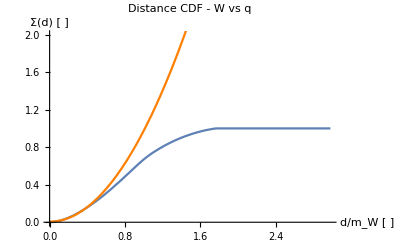

```mathematica
smalldfitfunc=Fit[NormedAUCqWtable[[;;15]],{1,d^2},{d}]
Show[{ListLinePlot[NormedAUCqWtable,AxesLabel->{"d/m_W [ ]","Σ(d) [ ]"},PlotLabel->"Distance CDF - W vs q",PlotRange->{0,2}],Plot[smalldfitfunc,{d,0,2.5},PlotStyle->Orange]}]
```

0.00858511+1.07973 d^2

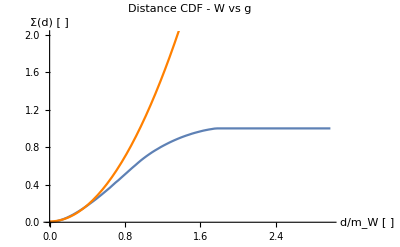

```mathematica
smalldfitfunc=Fit[NormedAUCgWtable[[;;15]],{1,d^2},{d}]
Show[{ListLinePlot[NormedAUCgWtable,AxesLabel->{"d/m_W [ ]","Σ(d) [ ]"},PlotRange->{0,2},PlotLabel->"Distance CDF - W vs g"],Plot[smalldfitfunc,{d,0,2.5},PlotStyle->Orange]}]
```

The small d fits also show us that there is little difference between the q and g background at leading order.

#### Test Plots at small d - Integrate - old

With Integrate

```mathematica
Σqofdtable =Monitor[Table[{d,GetΣqofd[d]},{d,1/8,3/8,1/(4 20)}],d];
```

-2.13127+1.97418 logd

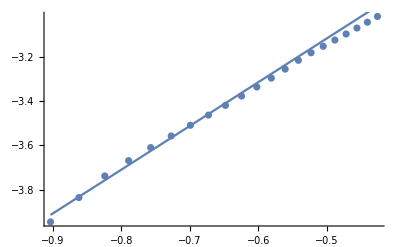

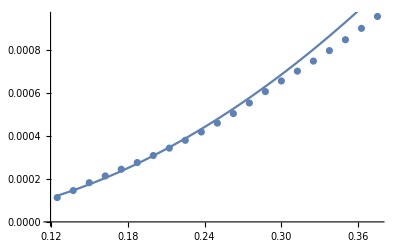

```mathematica
smalldfitfunc=Fit[(Log10@Σqofdtable)[[;;10]],{1,logd},{logd}]
Show[{ListPlot[Log10@Σqofdtable],Plot[%,{logd,Log10@(1/8),Log10@(3/8)}]}]
Show[{ListPlot[Σqofdtable],Plot[10^(%%/.logd->Log10[d]),{d,1/8,3/8}]}]
```

```mathematica
Σqofdtablesmaller =Monitor[Table[{d,GetΣqofd[d]},{d,0.01,0.2,0.01}],d];
```

-3.45655+0.679395 logd

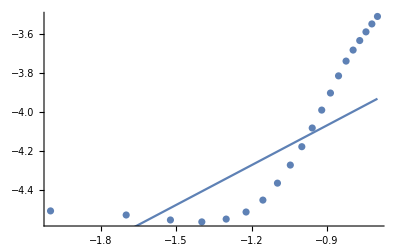

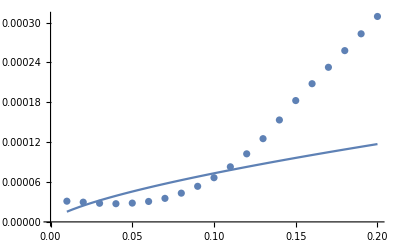

```mathematica
smalldfitfunc=Fit[(Log10@Σqofdtablesmaller)[[;;15]],{1,logd},{logd}]
Show[{ListPlot[Log10@Σqofdtablesmaller],Plot[%,{logd,Log10@0.01,Log10@0.2}]}]
Show[{ListPlot[Σqofdtablesmaller],Plot[10^(%%/.logd->Log10[d]),{d,0.01,0.2}]}]
```

#### Test Plots at small d - NIntegrate - old

With NIntegrate

```mathematica
Σqofdtable =Monitor[Table[{d,GetΣqofd[d]},{d,1/8,3/8,1/(4 20)}],d];
```

-1.81683+1.99361 logd

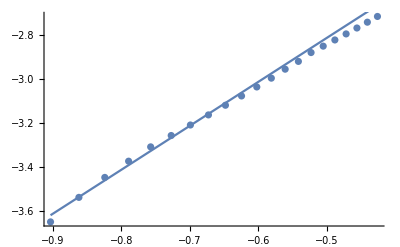

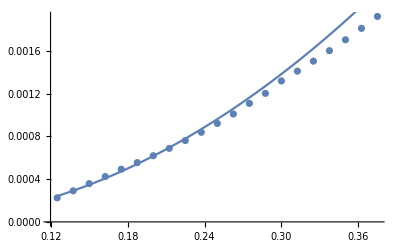

```mathematica
smalldfitfunc=Fit[(Log10@Σqofdtable)[[;;10]],{1,logd},{logd}]
Show[{ListPlot[Log10@Σqofdtable],Plot[%,{logd,Log10@(1/8),Log10@(3/8)}]}]
Show[{ListPlot[Σqofdtable],Plot[10^(%%/.logd->Log10[d]),{d,1/8,3/8}]}]
```

```mathematica
Σqofdtablesmaller =Monitor[Table[{d,GetΣqofd[d]},{d,0.01,0.2,0.01}],d];
```

-3.18707+0.647441 logd

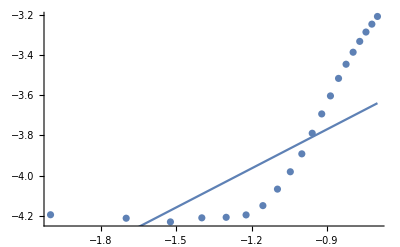

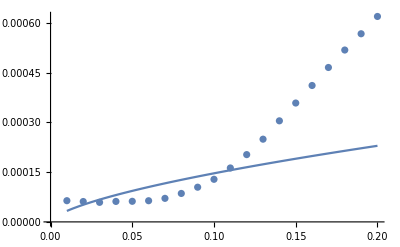

```mathematica
smalldfitfunc=Fit[(Log10@Σqofdtablesmaller)[[;;15]],{1,logd},{logd}]
Show[{ListPlot[Log10@Σqofdtablesmaller],Plot[%,{logd,Log10@0.01,Log10@0.2}]}]
Show[{ListPlot[Σqofdtablesmaller],Plot[10^(%%/.logd->Log10[d]),{d,0.01,0.2}]}]
```

-1.94987+1.85529 logd

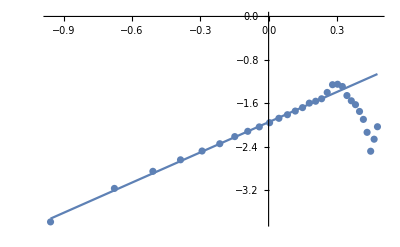

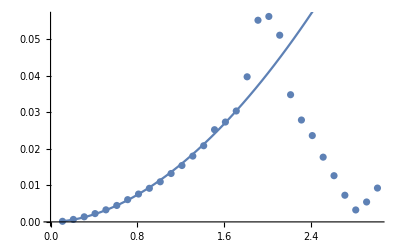

```mathematica
"W NIntegrate"
ΣqofdtableLargeRange =Monitor[Table[{d,GetΣqofd[d]},{d,0.11,3.01,0.1}],d];
smalldfitfunc=Fit[(Log10@ΣqofdtableLargeRange)[[;;15]],{1,logd},{logd}]
Show[{ListPlot[Log10@ΣqofdtableLargeRange],Plot[%,{logd,Log10@0.11,Log10@3.01}]}]
Show[{ListPlot[ΣqofdtableLargeRange],Plot[10^(%%/.logd->Log10[d]),{d,0.11,3.01}]}]
```

W Integrate

-1.95016+1.85135 logd

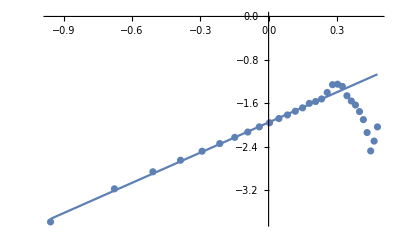

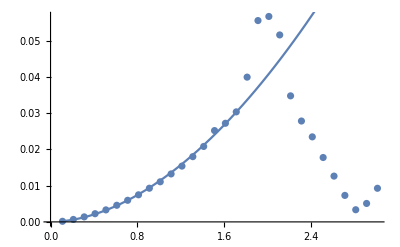

```mathematica
"W Integrate"
ΣqofdtableLargeRange =Monitor[Table[{d,GetΣqofd[d]},{d,0.11,3.01,0.1}],d];
smalldfitfunc=Fit[(Log10@ΣqofdtableLargeRange)[[;;15]],{1,logd},{logd}]
Show[{ListPlot[Log10@ΣqofdtableLargeRange],Plot[%,{logd,Log10@0.11,Log10@3.01}]}]
Show[{ListPlot[ΣqofdtableLargeRange],Plot[10^(%%/.logd->Log10[d]),{d,0.11,3.01}]}]
```

#### Plot the CDFs (and fit to parabolas)

```mathematica
smalldfitfunc=Fit[NormedAUCqWtable[[;;15]],{1,d^2},{d}]
Show[{ListLinePlot[NormedAUCqWtable,AxesLabel->{"d/m_W [ ]","Σ(d) [ ]"},PlotLabel->"Distance CDF (compared to parabola)- W vs q",PlotRange->{{0,0.5},{0,0.3}}],Plot[smalldfitfunc,{d,0,2.5},PlotStyle->Orange]}]
```

0.00629337+0.970957 d^2

-Graphics-

```mathematica
smalldfitfunc=Fit[NormedAUCqWtable[[;;15]],{1,d^2},{d}]
Show[{ListLinePlot[NormedAUCqWtable,AxesLabel->{"d/m_W [ ]","Σ(d) [ ]"},PlotLabel->"Distance CDF - W vs q",PlotRange->{0,2}],Plot[smalldfitfunc,{d,0,2.5},PlotStyle->Orange]}]
```

0.00629337+0.970957 d^2

-Graphics-

```mathematica
smalldfitfunc=Fit[NormedAUCgWtable[[;;15]],{1,d^2},{d}]
Show[{ListLinePlot[NormedAUCgWtable,AxesLabel->{"d/m_W [ ]","Σ(d) [ ]"},PlotRange->{0,2},PlotLabel->"Distance CDF - W vs g"],Plot[smalldfitfunc,{d,0,2.5},PlotStyle->Orange]}]
```

0.00858511+1.07973 d^2

-Graphics-

The small d fits also show us that there is little difference between the q and g background at leading order.